```mathematica
SetDirectory["/Users/danikaluntz-martin/Desktop/Advanced Lab/DoubleSlit-ED"];
countsfar1 = Import["20141122_single_slit_far.csv"];
countsfar1;
ListPlot[countsfar1, AxesLabel->{Distance (mm), Counts}];
```

```mathematica
θ = (x - x0)/R;
α = π * a * Sin[θ]/λ;
β = π * d * Sin[θ]/λ; 

Subscript[i, 2] = i0/4 * (Sinc[α])^2 ;

x0= 5.8;
a = 0.085;
d = 0.343;
R = 500;
λ = .000546;
```

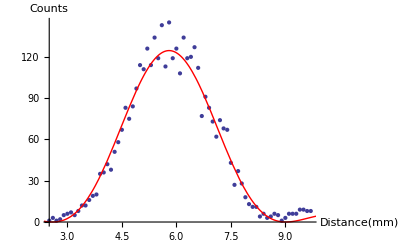

```mathematica
fitfar1 = NonlinearModelFit[countsfar1,Subscript[i, 2],{i0}, x];
plotfar1 = Plot[fitfar1[x], {x, -10, 10}];
plotfarb=Plot[0.21642509498661616 (575.4539524532704+0.0023980364459083407 ) Sinc[489.0757794050044Sin[1/500 (-5.8+x)]]^2,{x,0,10},PlotStyle->Red];
Show[ListPlot[countsfar1], plotfarb, AxesLabel-> {Distance [mm], Counts}]
```